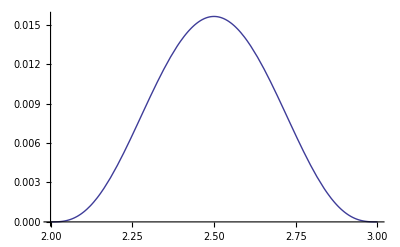

```mathematica
Plot[(x-2)^3*(3-x)^3,{x,2,3}]
```

```mathematica
bump[x_]=(x-s)^3*(t-x)^3
```

(t-x)^3 (-s+x)^3

```mathematica
b1[x_]=D[bump[x],x]
```

3 (t-x)^3 (-s+x)^2-3 (t-x)^2 (-s+x)^3

```mathematica
b1[s]
```

0

```mathematica
b1[t]
```

0

```mathematica
b2[x_]=D[b1[x],x]
```

6 (t-x)^3 (-s+x)-18 (t-x)^2 (-s+x)^2+6 (t-x) (-s+x)^3

```mathematica
b2[s]
```

0

```mathematica
b2[t]
```

0

```mathematica
b3[x_]=D[b2[x],x]
```

6 (t-x)^3-54 (t-x)^2 (-s+x)+54 (t-x) (-s+x)^2-6 (-s+x)^3

```mathematica
Integrate[bump[x],{x,s,t}]
```

-1/140 (s-t)^7

```mathematica
s=0.3;t=0.7;
```

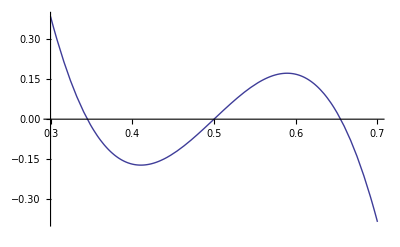

```mathematica
Plot[b3[x],{x,s,t}]
```

```mathematica
Clear[s,t]
```

```mathematica
b4[x_]=D[b3[x],x]
```

-72 (t-x)^2+216 (t-x) (-s+x)-72 (-s+x)^2

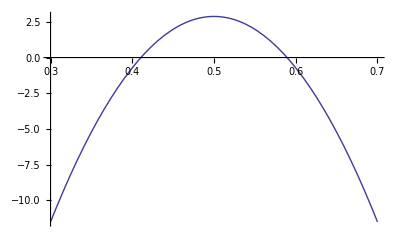

```mathematica
Plot[b4[x],{x,s,t}]
```

```mathematica
Solve[b4[x]==0,x]
```

{{x→1/10 (5 s+5 t-√5 √(s^2-2 s t+t^2))},{x→1/10 (5 s+5 t+√5 √(s^2-2 s t+t^2))}}

```mathematica
a=(5s+5t-Sqrt[5]*(t-s))/10
```

1/10 (5 s+5 t-√5 (-s+t))

```mathematica
Simplify[b4[a]]
```

0

```mathematica
b=(5s+5t+Sqrt[5]*(t-s))/10
```

1/10 (5 s+5 t+√5 (-s+t))

```mathematica
Simplify[b4[b]]
```

0

```mathematica
b3[s]
```

6 (-s+t)^3

```mathematica
b3[t]
```

-6 (-s+t)^3

```mathematica
Simplify[b3[a]]
```

(6 (s-t)^3)/(√5)

```mathematica
Simplify[b3[b]]
```

-(6 (s-t)^3)/(√5)

```mathematica
peak[x_,t_,h_]=h-Abs[x-t-h]
```

h-Abs[-h-t+x]

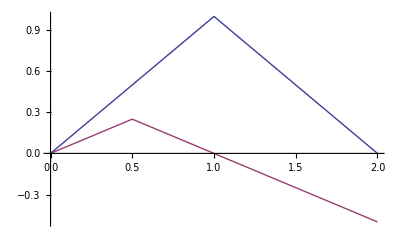

```mathematica
Plot[{peak[x,0,1],0.5peak[x,0,0.5]},{x,0,2}]
```